```mathematica
({{-1, 1, □, 1, 1, □, □, 0, 0, □, □, 0, □, □}, {1, -1, 1, 1, □, 1, □, 0, 0, 0, □, □, 0, □}, {□, 1, -1, 1, □, □, 1, □, □, 0, 0, □, 0, □}, {1, 1, 1, -1, 1, □, 1, □, 0, 0, 0, 0, □, 0}, {1, □, □, 1, -1, 1, □, 0, □, □, □, 0, □, 0}, {□, 1, □, □, 1, -1, 1, 0, □, □, □, □, 0, 0}, {□, □, 1, 1, □, 1, -1, □, □, □, 0, □, 0, 0}, {0, 0, □, □, 0, 0, □, -1, 1, □, □, 1, 1, 1}, {0, 0, □, 0, □, □, □, 1, -1, 1, □, 1, □, □}, {□, 0, 0, 0, □, □, □, □, 1, -1, 1, □, 1, □}, {□, □, 0, 0, □, □, 0, □, □, 1, -1, □, 1, 1}, {0, □, □, 0, 0, □, □, 1, 1, □, □, -1, □, 1}, {□, 0, 0, □, □, 0, 0, 1, □, 1, 1, □, -1, 1}, {□, □, □, 0, 0, 0, 0, 1, □, □, 1, 1, 1, -1}})

bilval[a_,b_]:=1/2((evars[[a,3]]^2+evars[[a,2]]^2-1)*(evars[[b,1]]+evars[[b,2]])/(evars[[a,1]]+evars[[a,2]])+(evars[[b,3]]^2+evars[[b,2]]^2-1)*(evars[[a,1]]+evars[[a,2]])/(evars[[b,1]]+evars[[b,2]]))-evars[[a,3]]*evars[[b,3]]-evars[[a,2]]*evars[[b,2]]

bil[a_,b_]:=1/2((vars[[a,3]]^2+vars[[a,2]]^2-1)*(vars[[b,1]]+vars[[b,2]])/(vars[[a,1]]+vars[[a,2]])+(vars[[b,3]]^2+vars[[b,2]]^2-1)*(vars[[a,1]]+vars[[a,2]])/(vars[[b,1]]+vars[[b,2]]))-vars[[a,3]]*vars[[b,3]]-vars[[a,2]]*vars[[b,2]]==matzeros[[a,b]]

matzeros=({{□, 1, □, □, □, 0, 0, □, □, □}, {1, □, 1, 1, □, 0, 0, 0, □, 0}, {□, 1, □, □, 1, □, □, 0, 0, 0}, {□, 1, □, □, 1, 0, □, □, □, 0}, {□, □, 1, 1, □, □, □, □, 0, 0}, {0, 0, □, 0, □, □, 1, □, □, 1}, {0, 0, □, □, □, 1, □, 1, □, □}, {□, 0, 0, □, □, □, 1, □, 1, 1}, {□, □, 0, □, 0, □, □, 1, □, 1}, {□, 0, 0, 0, 0, 1, □, 1, 1, □}})
vars=({{1, 1, a141}, {1, a52, a142}, {1, a53, a143}, {a46, 1, 0}, {1, a57, 0}, {a48, 0, 1}, {0, a59, a149}, {0, a510, a1410}, {0, a511, 1}, {a413, a513, 1}})
Solve[bil[1,2]&&bil[1,6]&&bil[1,7]&&bil[2,3]&&bil[2,4]&&bil[2,6]&&bil[2,7]&&bil[2,8]&&bil[2,10]&&bil[3,5]&&bil[3,8]&&bil[3,9]&&bil[3,10]&&bil[4,5]&&bil[4,6]&&bil[4,10]&&bil[5,9]&&bil[5,10]&&bil[6,7]&&bil[6,10]&&bil[7,8]&&bil[8,9]&&bil[8,10]&&bil[9,10]]
```

```mathematica
bil[1,2]&&bil[1,6]&&bil[1,7]&&bil[2,3]&&bil[2,4]&&bil[2,6]&&bil[2,7]&&bil[2,8]&&bil[2,10]&&bil[3,5]&&bil[3,8]&&bil[3,9]&&bil[3,10]&&bil[4,5]&&bil[4,6]&&bil[4,10]&&bil[5,9]&&bil[5,10]&&bil[6,7]&&bil[6,10]&&bil[7,8]&&bil[8,9]&&bil[8,10]&&bil[9,10]
```

-a141 a142-a52+1/2 (1/2 a141^2 (1+a52)+(2 (-1+a142^2+a52^2))/(1+a52))==1&&-a141+(a141^2 a48)/4==0&&-a141 a149-a59+1/2 ((a141^2 a59)/2+(2 (-1+a149^2+a59^2))/a59)==0&&-a142 a143-a52 a53+1/2 (((-1+a142^2+a52^2) (1+a53))/(1+a52)+((1+a52) (-1+a143^2+a53^2))/(1+a53))==1&&-a52+((1+a46) (-1+a142^2+a52^2))/(2 (1+a52))==1&&-a142+(a48 (-1+a142^2+a52^2))/(2 (1+a52))==0&&-a142 a149-a52 a59+1/2 (((-1+a142^2+a52^2) a59)/(1+a52)+((1+a52) (-1+a149^2+a59^2))/a59)==0&&-a1410 a142-a510 a52+1/2 (((-1+a1410^2+a510^2) (1+a52))/a510+(a510 (-1+a142^2+a52^2))/(1+a52))==0&&-a142-a513 a52+1/2 ((a513^2 (1+a52))/(a413+a513)+((a413+a513) (-1+a142^2+a52^2))/(1+a52))==0&&-a53 a57+1/2 (((-1+a143^2+a53^2) (1+a57))/(1+a53)+((1+a53) (-1+a57^2))/(1+a57))==1&&-a1410 a143-a510 a53+1/2 (((-1+a1410^2+a510^2) (1+a53))/a510+(a510 (-1+a143^2+a53^2))/(1+a53))==0&&-a143-a511 a53+1/2 (a511 (1+a53)+(a511 (-1+a143^2+a53^2))/(1+a53))==0&&-a143-a513 a53+1/2 ((a513^2 (1+a53))/(a413+a513)+((a413+a513) (-1+a143^2+a53^2))/(1+a53))==0&&-a57+((1+a46) (-1+a57^2))/(2 (1+a57))==1&&-a513+((1+a46) a513^2)/(2 (a413+a513))==0&&-a511 a57+1/2 (a511 (1+a57)+(a511 (-1+a57^2))/(1+a57))==0&&-a513 a57+1/2 ((a513^2 (1+a57))/(a413+a513)+((a413+a513) (-1+a57^2))/(1+a57))==0&&-a149+(a48 (-1+a149^2+a59^2))/(2 a59)==1&&-1+(a48 a513^2)/(2 (a413+a513))==1&&-a1410 a149-a510 a59+1/2 (((-1+a1410^2+a510^2) a59)/a510+(a510 (-1+a149^2+a59^2))/a59)==1&&-a1410-a510 a511+1/2 (a510 a511+((-1+a1410^2+a510^2) a511)/a510)==1&&-a1410-a510 a513+1/2 ((a510 a513^2)/(a413+a513)+((-1+a1410^2+a510^2) (a413+a513))/a510)==1&&-1-a511 a513+1/2 ((a511 a513^2)/(a413+a513)+a511 (a413+a513))==1

```mathematica
{a141,a1410,a142,a143,a149,a413,a46,a48,a510,a511,a513,a52,a53,a57,a59}/.%32
```

{{-2.61313,2.41421,-1.84776,-2.61313,2.41421,-1.53073,1.82843,-1.53073,-6.30864,-8.92177,-3.69552,2.41421,10.6569,5.82843,-2.61313},{-1.08239,-0.414214,0.765367,-1.08239,-0.414214,-3.69552,-3.82843,-3.69552,0.448342,-0.634051,1.53073,-0.414214,-0.656854,0.171573,-1.08239},{1.08239,-0.414214,-0.765367,1.08239,-0.414214,3.69552,-3.82843,3.69552,-0.448342,0.634051,-1.53073,-0.414214,-0.656854,0.171573,1.08239},{2.61313,2.41421,1.84776,2.61313,2.41421,1.53073,1.82843,1.53073,6.30864,8.92177,3.69552,2.41421,10.6569,5.82843,2.61313}}

```mathematica
RootApproximant[{2.613125929752752,2.4142135623730954,1.8477590650225744,2.613125929752752,2.4142135623730954,1.530733729460355,1.8284271247461907,1.530733729460355,6.308644059797901,8.921769989550652,3.6955181300451487,2.4142135623730954,10.656854249492381,5.828427124746191,2.613125929752752}]
```

{Root2.61Root[8-8 #1^2+#1^4&,4]2.613125929752753,1+√2,Root1.85Root[2-4 #1^2+#1^4&,4]1.8477590650225735,Root2.61Root[8-8 #1^2+#1^4&,4]2.613125929752753,1+√2,Root1.53Root[32-16 #1^2+#1^4&,3]1.5307337294603591,-1+2 √2,Root1.53Root[32-16 #1^2+#1^4&,3]1.5307337294603591,Root6.31Root[8-40 #1^2+#1^4&,4]6.3086440597979,Root8.92Root[32-80 #1^2+#1^4&,4]8.921769989550652,Root3.70Root[32-16 #1^2+#1^4&,4]3.695518130045147,1+√2,5+4 √2,3+2 √2,Root2.61Root[8-8 #1^2+#1^4&,4]2.613125929752753}

```mathematica
Solve[bil[1,2]&&bil[1,6]&&bil[1,7]&&bil[2,3]&&bil[2,4]&&bil[2,6]&&bil[2,7]&&bil[2,8]&&bil[2,10]&&bil[3,5]&&bil[3,8]&&bil[3,9]&&bil[3,10]&&bil[4,5]&&bil[4,6]&&bil[4,10]&&bil[5,9]&&bil[5,10]&&bil[6,7]&&bil[6,10]&&bil[7,8]&&bil[8,9]&&bil[8,10]&&bil[9,10]]
```

{{a141→-4 √(2-√2)+(2-√2)^(3/2),a1410→1+√2,a142→-3 √(2-√2)+(2-√2)^(3/2),a143→-4 √(2-√2)+(2-√2)^(3/2),a149→1+√2,a413→-2 √(2-√2),a46→-1+2 √2,a48→-2 √(2-√2),a510→-10 √(2-√2)+3 (2-√2)^(3/2),a511→2 (-7 √(2-√2)+2 (2-√2)^(3/2)),a513→2 (-3 √(2-√2)+(2-√2)^(3/2)),a52→1+√2,a53→5+4 √2,a57→3+2 √2,a59→-4 √(2-√2)+(2-√2)^(3/2)},{a141→4 √(2-√2)-(2-√2)^(3/2),a1410→1+√2,a142→3 √(2-√2)-(2-√2)^(3/2),a143→4 √(2-√2)-(2-√2)^(3/2),a149→1+√2,a413→2 √(2-√2),a46→-1+2 √2,a48→2 √(2-√2),a510→10 √(2-√2)-3 (2-√2)^(3/2),a511→2 (7 √(2-√2)-2 (2-√2)^(3/2)),a513→2 (3 √(2-√2)-(2-√2)^(3/2)),a52→1+√2,a53→5+4 √2,a57→3+2 √2,a59→4 √(2-√2)-(2-√2)^(3/2)},{a141→-4 √(2+√2)+(2+√2)^(3/2),a1410→1-√2,a142→-3 √(2+√2)+(2+√2)^(3/2),a143→-4 √(2+√2)+(2+√2)^(3/2),a149→1-√2,a413→-2 √(2+√2),a46→-1-2 √2,a48→-2 √(2+√2),a510→-10 √(2+√2)+3 (2+√2)^(3/2),a511→2 (-7 √(2+√2)+2 (2+√2)^(3/2)),a513→2 (-3 √(2+√2)+(2+√2)^(3/2)),a52→1-√2,a53→5-4 √2,a57→3-2 √2,a59→-4 √(2+√2)+(2+√2)^(3/2)},{a141→4 √(2+√2)-(2+√2)^(3/2),a1410→1-√2,a142→3 √(2+√2)-(2+√2)^(3/2),a143→4 √(2+√2)-(2+√2)^(3/2),a149→1-√2,a413→2 √(2+√2),a46→-1-2 √2,a48→2 √(2+√2),a510→10 √(2+√2)-3 (2+√2)^(3/2),a511→2 (7 √(2+√2)-2 (2+√2)^(3/2)),a513→2 (3 √(2+√2)-(2+√2)^(3/2)),a52→1-√2,a53→5-4 √2,a57→3-2 √2,a59→4 √(2+√2)-(2+√2)^(3/2)}}

```mathematica
Clear[a141,a1410,a142,a143,a149,a413,a46,a48,a510,a511,a513,a52,a53,a57,a59]
```

```mathematica
N[%35]
```

{{a141→-2.61313,a1410→2.41421,a142→-1.84776,a143→-2.61313,a149→2.41421,a413→-1.53073,a46→1.82843,a48→-1.53073,a510→-6.30864,a511→-8.92177,a513→-3.69552,a52→2.41421,a53→10.6569,a57→5.82843,a59→-2.61313},{a141→2.61313,a1410→2.41421,a142→1.84776,a143→2.61313,a149→2.41421,a413→1.53073,a46→1.82843,a48→1.53073,a510→6.30864,a511→8.92177,a513→3.69552,a52→2.41421,a53→10.6569,a57→5.82843,a59→2.61313},{a141→-1.08239,a1410→-0.414214,a142→0.765367,a143→-1.08239,a149→-0.414214,a413→-3.69552,a46→-3.82843,a48→-3.69552,a510→0.448342,a511→-0.634051,a513→1.53073,a52→-0.414214,a53→-0.656854,a57→0.171573,a59→-1.08239},{a141→1.08239,a1410→-0.414214,a142→-0.765367,a143→1.08239,a149→-0.414214,a413→3.69552,a46→-3.82843,a48→3.69552,a510→-0.448342,a511→0.634051,a513→-1.53073,a52→-0.414214,a53→-0.656854,a57→0.171573,a59→1.08239}}

```mathematica
{a141,a1410,a142,a143,a149,a413,a46,a48,a510,a511,a513,a52,a53,a57,a59}={4 √(2-√2)-(2-√2)^(3/2),1+√2,3 √(2-√2)-(2-√2)^(3/2),4 √(2-√2)-(2-√2)^(3/2),1+√2,2 √(2-√2),-1+2 √2,2 √(2-√2),10 √(2-√2)-3 (2-√2)^(3/2),2 (7 √(2-√2)-2 (2-√2)^(3/2)),2 (3 √(2-√2)-(2-√2)^(3/2)),1+√2,5+4 √2,3+2 √2,4 √(2-√2)-(2-√2)^(3/2)}
```

```mathematica
Simplify[{4 √(2-√2)-(2-√2)^(3/2),1+√2,3 √(2-√2)-(2-√2)^(3/2),4 √(2-√2)-(2-√2)^(3/2),1+√2,2 √(2-√2),-1+2 √2,2 √(2-√2),10 √(2-√2)-3 (2-√2)^(3/2),2 (7 √(2-√2)-2 (2-√2)^(3/2)),2 (3 √(2-√2)-(2-√2)^(3/2)),1+√2,5+4 √2,3+2 √2,4 √(2-√2)-(2-√2)^(3/2)}]
```

```mathematica
{a141,a1410,a142,a143,a149,a413,a46,a48,a510,a511,a513,a52,a53,a57,a59}={√(2-√2) (2+√2),1+√2,√(2-√2) (1+√2),√(2-√2) (2+√2),1+√2,2 √(2-√2),-1+2 √2,2 √(2-√2),√(2-√2) (4+3 √2),2 √(2-√2) (3+2 √2),2 √(2-√2) (1+√2),1+√2,5+4 √2,3+2 √2,√(2-√2) (2+√2)}
```

{√(2-√2) (2+√2),1+√2,√(2-√2) (1+√2),√(2-√2) (2+√2),1+√2,2 √(2-√2),-1+2 √2,2 √(2-√2),√(2-√2) (4+3 √2),2 √(2-√2) (3+2 √2),2 √(2-√2) (1+√2),1+√2,5+4 √2,3+2 √2,√(2-√2) (2+√2)}

```mathematica
bilval[a_,b_]:=1/2((evars[[a,3]]^2+evars[[a,2]]^2-1)*(evars[[b,1]]+evars[[b,2]])/(evars[[a,1]]+evars[[a,2]])+(evars[[b,3]]^2+evars[[b,2]]^2-1)*(evars[[a,1]]+evars[[a,2]])/(evars[[b,1]]+evars[[b,2]]))-evars[[a,3]]*evars[[b,3]]-evars[[a,2]]*evars[[b,2]]
```

```mathematica
evars=({{1, 1, a141}, {1, a52, a142}, {1, a53, a143}, {-1, 1, 0}, {1, -1, 0}, {a46, 1, 0}, {1, a57, 0}, {a48, 0, 1}, {0, a59, a149}, {0, a510, a1410}, {0, a511, 1}, {0, 0, 1}, {a413, a513, 1}, {0, 0, -1}})
```

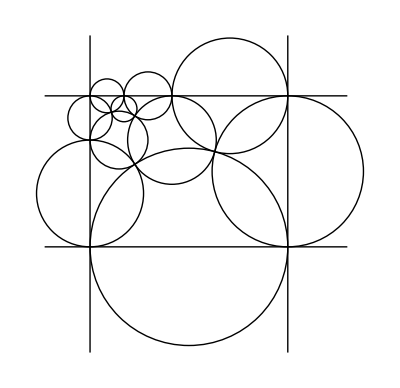

√(2-√2) (2+√2)

```mathematica
Graphics[{Table[Circle[{vars[[i,3]]/(vars[[i,1]]+vars[[i,2]]),vars[[i,2]]/(vars[[i,1]]+vars[[i,2]])},1/(vars[[i,1]]+vars[[i,2]])],{i,Length[vars]}],Line[{{0,-0.7},{0,1.4}}],Line[{{1.7,0},{-0.3,0}}],Line[{{1.7,1},{-0.3,1}}],Line[{{a141/2,-0.7},{a141/2,1.4}}]}]
```

```mathematica
bilval[6,13]
N[2/149(26+Sqrt[853374])]
```

-2 √(2-√2) (1+√2)+(4 √2 (2-√2) (1+√2)^2)/(2 √(2-√2)+2 √(2-√2) (1+√2))

12.7488

```mathematica
Simplify[bilval[1,11]]
```

2 √(2-√2) (4+3 √2)

√(2 (2+√2))

2 √(2-√2)+√(2 (2-√2))